## Position from Velocity — Using Associations

## January 16, 2025

Study Sections 4-6 of EIWL3 before working through this notebook.

### Associations

A limitation of Nest and NestList may have already caught your eye: the function you are compounding can only take one argument. When we are studying particle motion, we needs lots of arguments: time, position, velocity. When we are studying the motion of multiple particles in three dimensions, we need positions and velocities for each particle and each of these positions and velocities themselves will have three components! So there is no way we are going to be able to get by with functions that take and return only one number (like the total number of heads in the “Heads or Tails” notebook).

There are lots of ways around this, but the easiest way I can think of is to use Associations. Here is an association that holds the current time and the current position of a particle moving in one dimension:

```mathematica
state = <|"time"->3600, "position"->10000|>
```

<|time→3600,position→10000|>

This is a single variable that holds two things! In this association, “time” and “position” are keys, and 3600 and 10000 are their respective values.

Of course I could have used a list like this:

```mathematica
stateAsAList ={3600,10000}
```

{3600,10000}

But then you have to remember that the first element of the list is the time and the second element is the position. The nice thing about associations is that you are forced by the notation to always be specific about which key-value pair of the association you are accessing.

Here is a function that adds 1 to the time and 1 to the position:

```mathematica
addOne[a_]:=(
newTime = a[["time"]]+1;
newPosition = a[["position"]]+1;
<|"time"->newTime, "position"->newPosition|>
)
```

Let’s see if it works:

```mathematica
addOne[<|"time"->3600, "position"->10000|>]
```

<|time→3601,position→10001|>

So we are now able to use Nest and NestList with functions that have multiple numbers in their arguments and return values, except that the numbers are bundled up in an association to get around the one-argument limitation:

```mathematica
NestList[addOne, <|"time"->3600, "position"->10000|>, 5]
```

{<|time→3600,position→10000|>,<|time→3601,position→10001|>,<|time→3602,position→10002|>,<|time→3603,position→10003|>,<|time→3604,position→10004|>,<|time→3605,position→10005|>}

### Numerical Integration

We will use the formulas we derived in the “Position from Velocity — Theory” notebook:

t_2=t_1+Δt

x(t_2)=x(t_1)+v(t_1+Δt/2)*Δt

### Constant Velocity

By far the simplest example is constant velocity. Let’s just have a constant velocity of 3 and a time step of 0.01.

```mathematica
move[a_]:=(newTime = a[["time"]]+0.1;
newPosition = a[["position"]]+ 3 * 0.1;
<|"time"->newTime, "position"->newPosition|>
)
```

By far the simplest example is constant velocity. Let’s just have a constant velocity of 3 and a time step of 0.1. Then we need to do 15 steps to get from 2.0 to 3.5. Where should we start the particle? How about at time 2.0 we say it was at position -2.0?

```mathematica
NestList[move,<|"time"->2.0, "position"->-2.0|>,15]
```

{<|time→2.,position→-2.|>,<|time→2.1,position→-1.7|>,<|time→2.2,position→-1.4|>,<|time→2.3,position→-1.1|>,<|time→2.4,position→-0.8|>,<|time→2.5,position→-0.5|>,<|time→2.6,position→-0.2|>,<|time→2.7,position→0.1|>,<|time→2.8,position→0.4|>,<|time→2.9,position→0.7|>,<|time→3.,position→1.|>,<|time→3.1,position→1.3|>,<|time→3.2,position→1.6|>,<|time→3.3,position→1.9|>,<|time→3.4,position→2.2|>,<|time→3.5,position→2.5|>}

By far the simplest example is constant velocity. Let’s just have a constant velocity of 3 and a time step of 0.1. Then we need to do 15 steps to get from 2.0 to 3.5. Where should we start the particle? How about at time 2.0 we say it was at position -2.0?

### A Bounce

Let’s have the particle go at constant velocity of 6 until the time is 3.0, and then bounce and go -6 after that:

```mathematica
bounce[a_]:=(
deltaT=0.01;
time = a[["time"]];
position = a[["position"]];
newTime = time+deltaT;
midpointTime =time +deltaT/2;
midpointVelocity = If[midpointTime<3.0,6, -6];
newPosition = position+ midpointVelocity * deltaT;
<|"time"->newTime, "position"->newPosition|>
)
```

I cranked down the Δt to 0.1, and so I am going to have to crank up the number of steps to 150, and I am going to suppress the output:

```mathematica
lotsaPositions = NestList[bounce,<|"time"->2.0, "position"->-2.0|>,150];
```

### Displaying the Bounce

```mathematica
allThePositions = lotsaPositions[[All,"position"]];
```

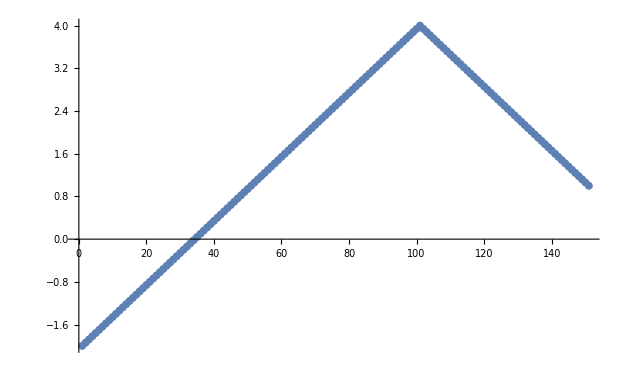

```mathematica
ListPlot[allThePositions]
```

The bounce at t=3.0 occurs at the 100th time step. The plot might look a little jaggy if viewed at low resolution, but it is entirely smooth when enlarged.